## Solution CP6: Systems of linear recurrence equations

Use Mathematica to verify your answers of the pen and paper practical.

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Solving recurrence equations with Mathematica

In Mathematica, the command RSolveValue[] is used for solving (systems of) recurrence equations. However, you will find not all systems can be solved this way; in such cases, you need to apply the method outlined in the manual and lectures, and solve the equations manually. Of course you can still use Mathematica, e.g. to calculate derivatives and to plot the solutions............ Also check out the command RecurrenceTable[] that enables you to iterate a first- or second-order recurrence equation, or a system of recurrence equations.

### Exercise 6-1

Consider the second-order recurrence equations z(t+2)=1/2 z(t+1)+1/2 z(t) and z(t+2)=2z(t+1)-2z(t).

(a) Solve both equations for z(0)=1 and z(1)=2.5

```mathematica
eq1=z[t+2]==0.5*z[t+1]+0.5*z[t]
eq2=z[t+2]==2z[t+1]-2z[t]
init={z[0]==1, z[1]==2.5};
```

z[2+t]==0.5 z[t]+0.5 z[1+t]

z[2+t]==-2 z[t]+2 z[1+t]

```mathematica
l11=(0.5+Sqrt[0.5^2+4*0.5])/2
l12=(0.5-Sqrt[0.5^2+4*0.5])/2
gSol1[A_, B_, t_]:=A*l11^t+B*l12^t
ab1=Flatten[SolveValues[gSol1[A, B, 0]==1 && gSol1[A, B,1]==2.5, {A, B}], 1]
gSol1[ab1[[1]], ab1[[2]], t]
```

1.

-0.5

{2.,-1.}

2.-1. (-0.5)^t

```mathematica
RSolveValue[eq1, z[t],t]
sol1=RSolveValue[{eq1, init}, z[t], t] // Simplify
```

(-0.5)^t C[1]+C[2]

2.-1. (-0.5)^t

```mathematica
l21=(2+Sqrt[2^2+4*(-2)])/2
l22=(2-Sqrt[2^2+4*(-2)])/2
gSol2[A_, B_, t_]:=A*l21^t+B*l22^t
ab2=Flatten[SolveValues[gSol2[A, B, 0]==1 && gSol2[A,B,1]==2.5,{A,B}],1]
gSol2[ab2[[1]], ab2[[2]], t]//ComplexExpand // Simplify
```

1+ⅈ

1-ⅈ

{0.5-0.75 ⅈ,0.5+0.75 ⅈ}

2^(t/2) (1. Cos[(π t)/4]+1.5 Sin[(π t)/4])

```mathematica
RSolveValue[eq2, z[t],t]
sol2=RSolveValue[{eq2, init}, z[t],t]//ComplexExpand // Simplify
```

(1-ⅈ)^t C[1]+(1+ⅈ)^t C[2]

2^(t/2) (1. Cos[(π t)/4]+1.5 Sin[(π t)/4])

(b) Calculate in both cases the values at time t=5.

```mathematica
gSol1[ab1[[1]], ab1[[2]], 5]
sol1/.t->5
sol1
```

2.03125

2.03125

2.-1. (-0.5)^t

```mathematica
gSol2[ab2[[1]], ab2[[2]], 5]
sol2/.t->5
```

-10.+0. ⅈ

-10.

(c) Plot the solution for both cases. What can you conclude about its behaviour over time?

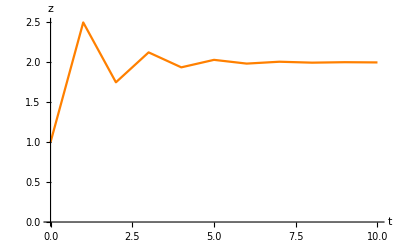

{1.,2.5,1.75,2.125,1.9375,2.03125,1.98438,2.00781,1.99609,2.00195,1.99902}

```mathematica
p1=ListLinePlot[Table[{t, sol1/.t->t},  {t, 0, 10}], PlotStyle->Orange, AxesLabel->{"t", "z"}]
RecurrenceTable[{eq1,z[0]==1, z[1]==2.5},z,{t,0,10}]
```

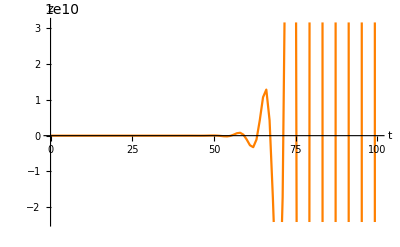

{1.,2.5,3.,1.,-4.,-10.,-12.,-4.,16.,40.,48.,16.,-64.,-160.,-192.,-64.,256.,640.,768.,256.,-1024.,-2560.,-3072.,-1024.,4096.,10240.,12288.,4096.,-16384.,-40960.,-49152.,-16384.,65536.,163840.,196608.,65536.,-262144.,-655360.,-786432.,-262144.,1.04858×10^6,2.62144×10^6,3.14573×10^6,1.04858×10^6,-4.1943×10^6,-1.04858×10^7,-1.25829×10^7,-4.1943×10^6,1.67772×10^7,4.1943×10^7,5.03316×10^7,1.67772×10^7,-6.71089×10^7,-1.67772×10^8,-2.01327×10^8,-6.71089×10^7,2.68435×10^8,6.71089×10^8,8.05306×10^8,2.68435×10^8,-1.07374×10^9,-2.68435×10^9,-3.22123×10^9,-1.07374×10^9,4.29497×10^9,1.07374×10^10,1.28849×10^10,4.29497×10^9,-1.71799×10^10,-4.29497×10^10,-5.15396×10^10,-1.71799×10^10,6.87195×10^10,1.71799×10^11,2.06158×10^11,6.87195×10^10,-2.74878×10^11,-6.87195×10^11,-8.24634×10^11,-2.74878×10^11,1.09951×10^12,2.74878×10^12,3.29853×10^12,1.09951×10^12,-4.39805×10^12,-1.09951×10^13,-1.31941×10^13,-4.39805×10^12,1.75922×10^13,4.39805×10^13,5.27766×10^13,1.75922×10^13,-7.03687×10^13,-1.75922×10^14,-2.11106×10^14,-7.03687×10^13,2.81475×10^14,7.03687×10^14,8.44425×10^14,2.81475×10^14,-1.1259×10^15}

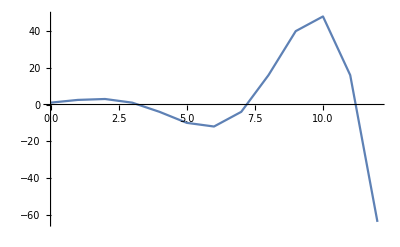

```mathematica
p2=ListLinePlot[Table[{t, sol2/.t->t}, {t, 0,100}], PlotStyle->Orange, AxesLabel->{"t", "z"}]
RecurrenceTable[{eq2, init}, z, {t, 0, 100}]
DiscretePlot[{sol2},{t,0,12},Joined->True, Filling->None]
```

### Exercise 6-2

Consider two systems of recurrence equations: 
(1)   x(t+1)=3x(t)-2y(t), y(t+1)=2x(t)-2y(t)
(2)   x(t+1)=1/2 x(t)-y(t), y(t+1)=x(t)+1/2 y(t)

(a)  Solve both systems for initial values x(0)=y(0)=1

```mathematica
sys1={x[t+1]==3x[t]-2y[t], y[t+1]==2x[t]-2y[t]};
sys2={x[t+1]==(1/2)*x[t]-y[t], y[t+1]==x[t]+(1/2)*y[t]};
init={x[0]==1, y[0]==1};
```

```mathematica
M1={{3, -2},{2, -2}};
l1=Flatten[SolveValues[l^2-Tr[M1]^2*l+Det[M1]==0,l],1]
genX1[A_, B_, t_]:=A*l1[[1]]^t+B*l1[[2]]^t
genY1[C_, D_, t_]:=C*l1[[1]]^t+D*l1[[2]]^t
ab1=Flatten[SolveValues[genX1[A, B,0]==1 && genX1[A, B, 1]==3-2,{A,B}],1]
cd1=Flatten[SolveValues[genY1[c, d,0]==1 && genY1[c, d, 1]==2-2,{c,d}],1]
genX1[ab1[[1]], ab1[[2]], t]
genY1[cd1[[1]], cd1[[2]], t]
```

{-1,2}

{1/3,2/3}

{2/3,1/3}

(-1)^t/3+2^(1+t)/3

(2 (-1)^t)/3+2^t/3

```mathematica
xy1=RSolveValue[{sys1, init},{x[t], y[t]},t]
```

{1/3 ((-1)^t+2^(1+t)),1/3 (2 (-1)^t+2^t)}

```mathematica
xy2=RSolveValue[{sys2, init}, {x[t], y[t]}, t]
{x2,y2}=RSolveValue[{sys2,init},{x[t],y[t]},t]
{x2,y2}=RSolveValue[{sys2,init},{x[t],y[t]},t]//ComplexExpand//Simplify
```

{(1+ⅈ) 2^(-1-t) (-ⅈ (1-2 ⅈ)^t+(1+2 ⅈ)^t),(1+ⅈ) 2^(-1-t) ((1-2 ⅈ)^t-ⅈ (1+2 ⅈ)^t)}

{(1+ⅈ) 2^(-1-t) (-ⅈ (1-2 ⅈ)^t+(1+2 ⅈ)^t),(1+ⅈ) 2^(-1-t) ((1-2 ⅈ)^t-ⅈ (1+2 ⅈ)^t)}

{2^-t 5^(t/2) (Cos[t ArcTan[2]]-Sin[t ArcTan[2]]),2^-t 5^(t/2) (Cos[t ArcTan[2]]+Sin[t ArcTan[2]])}

(b) Calculate x(5) and y(5)  for both sets of solutions

```mathematica
xy1/.t->5
xy2/.t->5
```

{21,10}

{2.46875+0. ⅈ,0.09375+0. ⅈ}

(c) Plot the solutions.for both systems

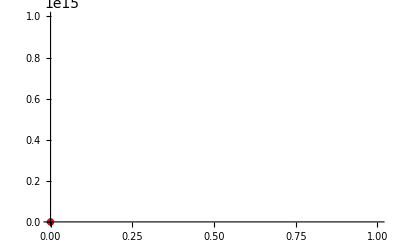

-Graphics-

-Graphics-

```mathematica
maxT=100;
p1=ListLinePlot[Table[xy1/.t->i, {i, 0,maxT}], PlotRange->Full];
iniPoint1=ListPlot[{xy1[[1]]/.t->0, xy1[[2]]/.t->0}, PlotStyle->Red];
Show[p1, iniPoint1]
px1=ListLinePlot[Table[{t, xy1[[1]]/.t->t}, {t, 0, maxT}], AxesLabel->{"t", "x"}]
py1=ListLinePlot[Table[{t, xy1[[2]]/.t->t}, {t,0,maxT}], PlotStyle->Orange, AxesLabel->{"t", "y"}]
```

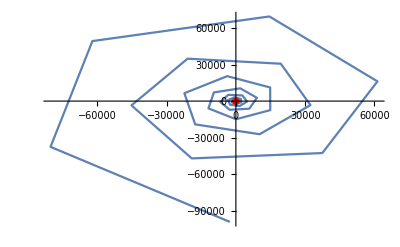

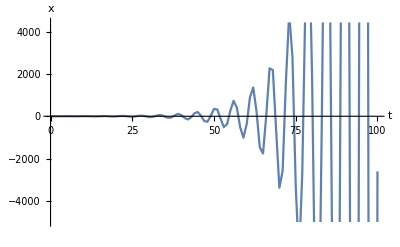

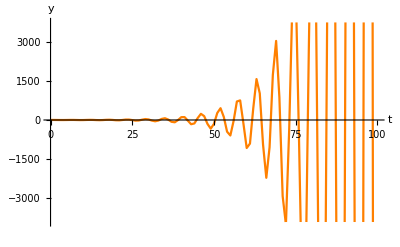

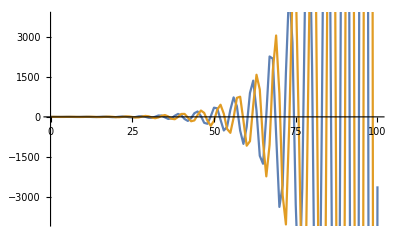

```mathematica
p2=ListLinePlot[Table[xy2/.t->i, {i, 0,maxT}], PlotRange->Full];
iniPoint2=ListPlot[{xy2[[1]]/.t->0, xy2[[2]]/.t->0}, PlotStyle->Red];
Show[p2, iniPoint2]
px2=ListLinePlot[Table[{t, xy2[[1]]/.t->t}, {t, 0, maxT}], AxesLabel->{"t", "x"}]
py2=ListLinePlot[Table[{t, xy2[[2]]/.t->t}, {t,0,maxT}], PlotStyle->Orange, AxesLabel->{"t", "y"}]
DiscretePlot[{x2, y2}, {t, 0, maxT}, Joined->True, Filling->None]
```

### Exercise 6-3

In this exercise, we will study a simple weather forecasting model based on the following assumptions:
- The weather has only two states: either the sun is shining or it is raining.
- Weather is a “Markov process”, i.e. a probability process in which the probability of a certain type of weather tomorrow only depends on today’s weather.
Finally, based on our past experience, we assume the relationship between today's weather and the next day's weather. If it’s sunny on any given day, the chance that it’ll be again sunny on the next day is 90%. If it rains on any given day, the chance that it will also rain on the next day is 50%. And, more importantly, we assume that these relationships are constant over time. 
z(t): chance of sun on day t
r(t): change of rain on day t
Consider the recurrence equations:
z(t+1)=0.9z(t)+0.5r(t)
r(t+1)=0.1z(t)+0.5r(t)

(a) Solve this system of recurrence equations and plot the solutions

```mathematica
sys={z[t+1]==0.9z[t]+0.5r[t], r[t+1]==0.1z[t]+0.5r[t]};
init={z[0]==z0, r[0]==r0}; 
{solZ, solR}=RSolveValue[{sys, init},{z[t], r[t]},t]
z0=1;r0=0; (*first day is fully sunny, no rain*)
{solZ, solR}
```

{-0.833333 (-1. r0+1. 0.4^t r0-1. z0-0.2 0.4^t z0),0.166667 5.^(-1. t) (5. 2.^t r0+1. 5.^(1. t) r0+1. 5.^(1. t) z0-1. 0.4^t 5.^(1. t) z0)}

{-0.833333 (-1.-0.2 0.4^t),0.166667 5.^(-1. t) (0.+1. 5.^(1. t)-1. 0.4^t 5.^(1. t))}

100

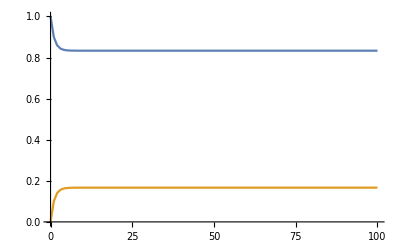

```mathematica
maxT=100 (*days*)
DiscretePlot[{solZ,solR}, {t, 0, maxT}, Joined->True, Filling->None, PlotRange->{{0, maxT}, {0,1}}]
```

(b) Implement the system from (a) as a second-order recurrence equation and solve it; plot the solution.

z[2+t]==-0.4 z[t]+1.4 z[1+t]

0.166667 (5.+1. 0.4^t)

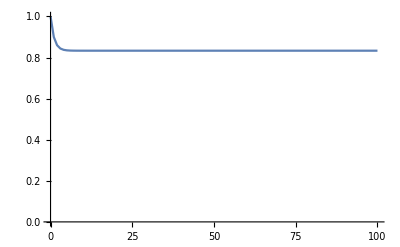

```mathematica
eqZ2=z[t+2]==1.4z[t+1]-0.4z[t]
solZ2 = RSolveValue[{eqZ2,z[0]==z0, z[1]==0.9z0+0.5r0}, z[t],t]
DiscretePlot[solZ2, {t, 0, maxT}, Joined->True, Filling->None, PlotRange->{{0, maxT}, {0,1}}]
```

r[2+t]==-0.4 r[t]+1.4 r[1+t]

-0.166667 (-1.+1. 0.4^t)

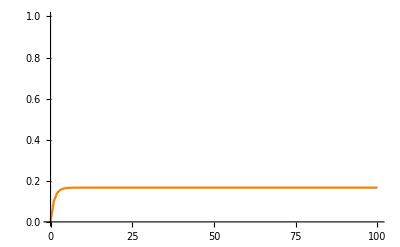

```mathematica
eqR2=r[t+2]==1.4r[t+1]-0.4r[t]
solR2 = RSolveValue[{eqR2,r[0]==r0, r[1]==0.1z0+0.5r0}, r[t],t]
DiscretePlot[solR2, {t, 0, maxT}, Joined->True, Filling->None, PlotRange->{{0, maxT}, {0,1}}, PlotStyle->Orange]
```

(c) Calculate the probability of nice weather next Saturday, i.e., z(4)

```mathematica
solZ2/.t->4
```

0.8376